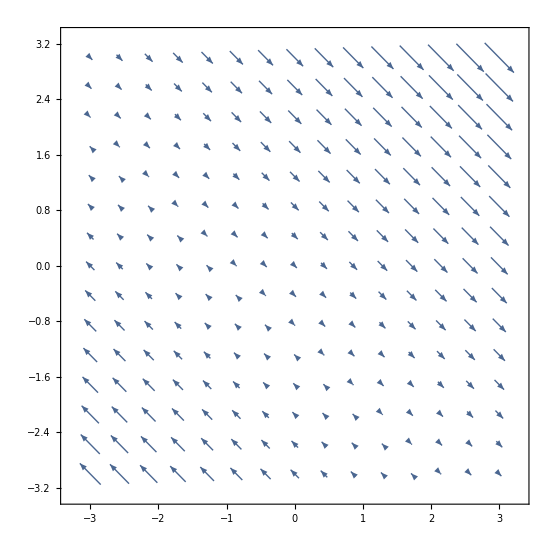

{{1/(√2),1/(√2)},{-1/(√2),-1/(√2)}}

-Graphics-

-Graphics-

```mathematica
V[x1_,y1_]:={(1+x+y)/(√2),-(1+x+y)/(√2)}/.x->x1/.y->y1
VectorPlot[{V[x,y]},{x,-3,3},{y,-3,3}]
gradV[x_,y_]:=Grad[V[x1,y1],{x1,y1}]/.x1->x/.y1->y
gradV[x,y]
VectorPlot[gradV[x,y].n,{x,-3,3},{y,-3,3}]
n={1,1}/Sqrt[2];
λ=1;
VectorPlot[V[x,y]-λ*gradV[x,y].n,{x,-3,3},{y,-3,3}]
```

```mathematica
gradV[x,y].n
```

{1,-1}

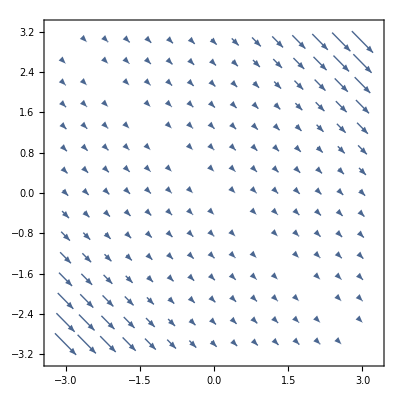

```mathematica
V[x_,y_]:={(y+x)^2,-(x+y)^2}
VectorPlot[V[x,y],{x,-3,3},{y,-3,3}]
```

```mathematica
V3D[x_,y_,z_]:={(y+x)^2,-(x+y)^2, 0}
VectorPlot3D[V3D[x,y,z],{x,-3,3},{y,-3,3},{z,-3,3},VectorColorFunction->"DeepSeaColors"]
```

-Graphics3D-

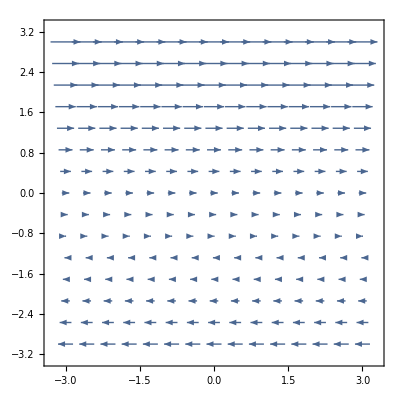

-π/4

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

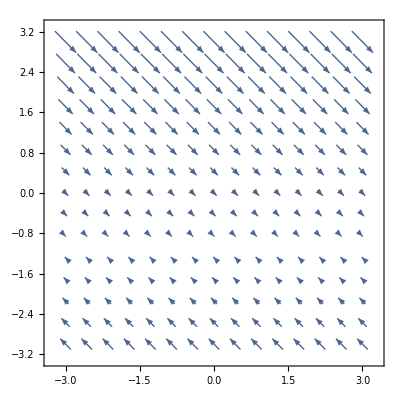

{{0,1},{0,0}}

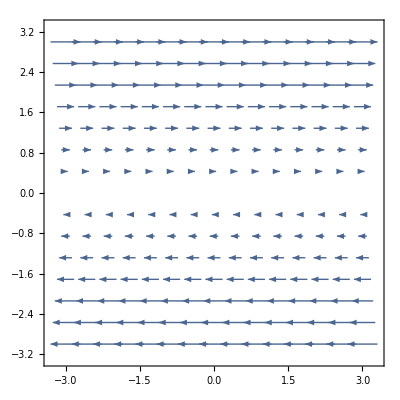

```mathematica
V[x_,y_]:={1+y,0}
VectorPlot[V[x,y],{x,-3,3},{y,-3,3}]
a=-Pi/4
A={{Cos[a],-Sin[a]},{Sin[a],Cos[a]}}
VectorPlot[A.V[x,y],{x,-3,3},{y,-3,3}]

gradV[x_,y_]:=Grad[V[x1,y1],{x1,y1}]/.x1->x/.y1->y
gradV[x,y]
n={0,1};
λ=1;
VectorPlot[V[x,y]-λ*gradV[x,y].n,{x,-3,3},{y,-3,3}]
```

```mathematica
V[1,0]
gradV[1,0].n
```

{1,0}

{1,0}

```mathematica
A.V[x,y]
```

{(1+y)/(√2),-(1+y)/(√2)}